## Matrix Element calculation

```mathematica
nmax = 15;η = 0.2; τ = 1/(1.84 10^6)
```

5.43478×10^-7

```mathematica
LaguerreL[r,s,t] //Expand
```

LaguerreL[r,s,t]

```mathematica
Min[1,2]
```

1

```mathematica
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
M[n_,nt_] :=NIntegrate[Sin[θ]/2 Abs[Sum[√((Min[n,m]!)/((Min[n,m]+Abs[m-n])!))(ⅈ η Cos[θ] )^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],(η Cos[θ])^2]Exp[-(η Cos[θ])^2/2] Dr[m,nt],{m,0,nmax}]]^2,{θ,0, Pi}]
```

```mathematica
Dr[1,1]
```

0.940991+0. ⅈ

```mathematica
M [3,3]
```

0.708382

```mathematica
DrMat = Table[Dr[n,nt],{n,0,nmax },{nt,0,nmax}] ;
```

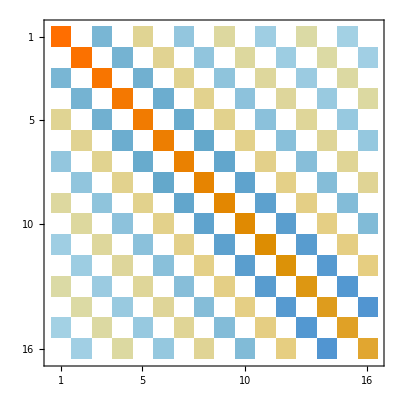

```mathematica
MatrixPlot[DrMat]
```

```mathematica
Table[ Sum[Abs[DrMat[[j,m]]]^2,{m,1,11}],{j,1,16}]
```

{1.,1.,1.,1.,1.,1.,1.,0.999969,0.998516,0.964967,0.680377,0.313077,0.0405458,0.00245716,0.0000887457,2.17738×10^-6}

```mathematica
Mat = Table[M[n,nt],{n,0,nmax},{nt,0,nmax}]
```

{{0.000500576,0.0115496+0. ⅈ,0.00106545,0.0000569671+0. ⅈ,2.13814×10^-6,6.1895×10^-8+0. ⅈ,1.47135×10^-9,2.99231×10^-11+0. ⅈ,5.34862×10^-13,8.55832×10^-15+0. ⅈ,1.242×10^-16,1.65079×10^-18+0. ⅈ,2.02499×10^-20,2.30691×10^-22+0. ⅈ,2.45348×10^-24,2.44696×10^-26+0. ⅈ},{0.0369755+0. ⅈ,0.854275,0.0890086+0. ⅈ,0.00638561,0.000324538+0. ⅈ,0.0000126444,3.98087×10^-7+0. ⅈ,1.04998×10^-8,2.3811×10^-10+0. ⅈ,4.73403×10^-12,8.37721×10^-14+0. ⅈ,1.33539×10^-15,1.93648×10^-17+0. ⅈ,2.57541×10^-19,3.16292×10^-21+0. ⅈ,3.60808×10^-23},{0.00165867,0.0890363+0. ⅈ,0.776546,0.120051+0. ⅈ,0.0117555,0.000759721+0. ⅈ,0.0000359313,1.33045×10^-6+0. ⅈ,4.03424×10^-8,1.03391×10^-9+0. ⅈ,2.29222×10^-11,4.47496×10^-13+0. ⅈ,7.80088×10^-15,1.22802×10^-16+0. ⅈ,1.76194×10^-18,2.32198×10^-20+0. ⅈ},{0.0000732674+0. ⅈ,0.00637046,0.120059+0. ⅈ,0.708382,0.145467+0. ⅈ,0.0181374,0.00142649+0. ⅈ,0.0000795059,3.38945×10^-6+0. ⅈ,1.16276×10^-7,3.3257×10^-9+0. ⅈ,8.13934×10^-11,1.7385×10^-12+0. ⅈ,3.29113×10^-14,5.59094×10^-16+0. ⅈ,8.60993×10^-18},{2.44933×10^-6+0. ⅈ,0.000324102+0. ⅈ,0.0117557+0. ⅈ,0.145467+0. ⅈ,0.649504+0. ⅈ,0.165266+0. ⅈ,0.0251786+0. ⅈ,0.00234313+0. ⅈ,0.00015077+0. ⅈ,7.28497×10^-6+0. ⅈ,2.79256×10^-7+0. ⅈ,8.82499×10^-9+0. ⅈ,2.36458×10^-10+0. ⅈ,5.48743×10^-12+0. ⅈ,1.12146×10^-13+0. ⅈ,2.04541×10^-15+0. ⅈ},{6.65305×10^-8+0. ⅈ,0.0000126358+0. ⅈ,0.000759727+0. ⅈ,0.0181374+0. ⅈ,0.165266+0. ⅈ,0.599102+0. ⅈ,0.180316+0. ⅈ,0.0326158+0. ⅈ,0.00351817+0. ⅈ,0.000257281+0. ⅈ,0.0000139165+0. ⅈ,5.90155×10^-7+0. ⅈ,2.04362×10^-8+0. ⅈ,5.95324×10^-10+0. ⅈ,1.49219×10^-11+0. ⅈ,3.27537×10^-13+0. ⅈ},{1.52788×10^-9+0. ⅈ,3.97959×10^-7+0. ⅈ,0.0000359314+0. ⅈ,0.00142649+0. ⅈ,0.0251786+0. ⅈ,0.180316+0. ⅈ,0.556067+0. ⅈ,0.191363+0. ⅈ,0.0402299+0. ⅈ,0.00495134+0. ⅈ,0.000406456+0. ⅈ,0.0000243668+0. ⅈ,1.13372×10^-6+0. ⅈ,4.27211×10^-8+0. ⅈ,1.34505×10^-9+0. ⅈ,3.62281×10^-11+0. ⅈ},{3.05103×10^-11+0. ⅈ,1.04982×10^-8+0. ⅈ,1.33045×10^-6+0. ⅈ,0.0000795059+0. ⅈ,0.00234313+0. ⅈ,0.0326158+0. ⅈ,0.191363+0. ⅈ,0.519412+0. ⅈ,0.199062+0. ⅈ,0.0478403+0. ⅈ,0.00663519+0. ⅈ,0.000605345+0. ⅈ,0.0000398899+0. ⅈ,2.02222×10^-6+0. ⅈ,8.24327×10^-8+0. ⅈ,2.79073×10^-9+0. ⅈ},{5.40196×10^-13+0. ⅈ,2.38093×10^-10+0. ⅈ,4.03424×10^-8+0. ⅈ,3.38945×10^-6+0. ⅈ,0.00015077+0. ⅈ,0.00351817+0. ⅈ,0.0402299+0. ⅈ,0.199062+0. ⅈ,0.488266+0. ⅈ,0.203986+0. ⅈ,0.0553007+0. ⅈ,0.00855655+0. ⅈ,0.00086045+0. ⅈ,0.0000618947+0. ⅈ,3.39868×10^-6+0. ⅈ,1.49105×10^-7+0. ⅈ},{8.60153×10^-15+0. ⅈ,4.73388×10^-12+0. ⅈ,1.03391×10^-9+0. ⅈ,1.16276×10^-7+0. ⅈ,7.28497×10^-6+0. ⅈ,0.000257281+0. ⅈ,0.00495134+0. ⅈ,0.0478403+0. ⅈ,0.203986+0. ⅈ,0.461856+0. ⅈ,0.206634+0. ⅈ,0.0624945+0. ⅈ,0.0106978+0. ⅈ,0.00117759+0. ⅈ,0.0000919246+0. ⅈ,5.4393×10^-6+0. ⅈ},{1.24517×10^-16+0. ⅈ,8.37708×10^-14+0. ⅈ,2.29222×10^-11+0. ⅈ,3.3257×10^-9+0. ⅈ,2.79256×10^-7+0. ⅈ,0.0000139165+0. ⅈ,0.000406456+0. ⅈ,0.00663519+0. ⅈ,0.0553007+0. ⅈ,0.206634+0. ⅈ,0.439503+0. ⅈ,0.207436+0. ⅈ,0.0693312+0. ⅈ,0.0130381+0. ⅈ,0.00156182+0. ⅈ,0.000131612+0. ⅈ},{1.6529×10^-18+0. ⅈ,1.33538×10^-15+0. ⅈ,4.47496×10^-13+0. ⅈ,8.13934×10^-11+0. ⅈ,8.82499×10^-9+0. ⅈ,5.90155×10^-7+0. ⅈ,0.0000243668+0. ⅈ,0.000605345+0. ⅈ,0.00855655+0. ⅈ,0.0624945+0. ⅈ,0.207436+0. ⅈ,0.420608+0. ⅈ,0.206766+0. ⅈ,0.0757421+0. ⅈ,0.0155547+0. ⅈ,0.00201636+0. ⅈ},{2.0263×10^-20+0. ⅈ,1.93647×10^-17+0. ⅈ,7.80088×10^-15+0. ⅈ,1.7385×10^-12+0. ⅈ,2.36458×10^-10+0. ⅈ,2.04362×10^-8+0. ⅈ,1.13372×10^-6+0. ⅈ,0.0000398899+0. ⅈ,0.00086045+0. ⅈ,0.0106978+0. ⅈ,0.0693312+0. ⅈ,0.206766+0. ⅈ,0.404647+0. ⅈ,0.204942+0. ⅈ,0.0816905+0. ⅈ,0.0181967+0. ⅈ},{2.30766×10^-22+0. ⅈ,2.57541×10^-19+0. ⅈ,1.22802×10^-16+0. ⅈ,3.29113×10^-14+0. ⅈ,5.48743×10^-12+0. ⅈ,5.95324×10^-10+0. ⅈ,4.27211×10^-8+0. ⅈ,2.02222×10^-6+0. ⅈ,0.0000618946+0. ⅈ,0.00117759+0. ⅈ,0.0130381+0. ⅈ,0.075742+0. ⅈ,0.20494+0. ⅈ,0.391128+0. ⅈ,0.202356+0. ⅈ,0.086753+0. ⅈ},{2.45388×10^-24+0. ⅈ,3.16291×10^-21+0. ⅈ,1.76194×10^-18+0. ⅈ,5.59094×10^-16+0. ⅈ,1.12146×10^-13+0. ⅈ,1.49219×10^-11+0. ⅈ,1.34505×10^-9+0. ⅈ,8.24327×10^-8+0. ⅈ,3.39868×10^-6+0. ⅈ,0.0000919249+0. ⅈ,0.00156184+0. ⅈ,0.0155551+0. ⅈ,0.081696+0. ⅈ,0.202316+0. ⅈ,0.378185+0. ⅈ,0.197798+0. ⅈ},{2.44716×10^-26+0. ⅈ,3.60808×10^-23+0. ⅈ,2.32198×10^-20+0. ⅈ,8.60992×10^-18+0. ⅈ,2.04541×10^-15+0. ⅈ,3.27536×10^-13+0. ⅈ,3.62279×10^-11+0. ⅈ,2.79069×10^-9+0. ⅈ,1.49101×10^-7+0. ⅈ,5.43888×10^-6+0. ⅈ,0.000131587+0. ⅈ,0.00201539+0. ⅈ,0.0181744+0. ⅈ,0.0864791+0. ⅈ,0.19473+0. ⅈ,0.349232+0. ⅈ}}

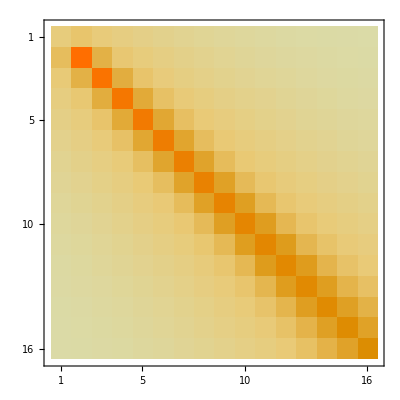

```mathematica
MatrixPlot[Mat]
```

```mathematica
<
```

```mathematica
Table[ Sum[Mat[[j,m]],{m,1,11}],{j,1,16}]
```

{0.0131748+0. ⅈ,0.986982+0. ⅈ,0.999845+0. ⅈ,0.999999+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999974+0. ⅈ,0.999353+0. ⅈ,0.990518+0. ⅈ,0.925532+0. ⅈ,0.708493+0. ⅈ,0.279117+0. ⅈ,0.0809305+0. ⅈ,0.0142796+0. ⅈ,0.00165724+0. ⅈ,0.000137178+0. ⅈ}

```mathematica
{0.9500066076371911+0. ⅈ,0.9981858353884894+0. ⅈ,0.9999252554603134+0. ⅈ,0.9999975389684228+0. ⅈ,0.9999999137599004+0. ⅈ,0.9999989443099998+0. ⅈ,0.9999639056062806+0. ⅈ,0.9991850718498525+0. ⅈ,0.9869398839062721+0. ⅈ,0.8466419397926749+0. ⅈ,0.11540074126484189+0. ⅈ}
Table[ Sum[M[j,m],{m,1,40}],{j,1,40}]
```

{0.950007+0. ⅈ,0.998186+0. ⅈ,0.999925+0. ⅈ,0.999998+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999964+0. ⅈ,0.999185+0. ⅈ,0.98694+0. ⅈ,0.846642+0. ⅈ,0.115401+0. ⅈ}

{0.980684,0.999521,0.999992,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999894,0.993787,0.84998,0.149262,0.00692783,0.000149055,1.88655×10^-6,1.59863×10^-8,9.83276×10^-11,4.63835×10^-13,1.74623×10^-15,5.40682×10^-18,1.40948×10^-20,3.15211×10^-23,6.1407×10^-26,1.05545×10^-28,1.61778×10^-31,2.23173×10^-34,2.79275×10^-37,3.1921×10^-40,3.3527×10^-43,3.25314×10^-46,2.92995×10^-49,2.45986×10^-52,1.93247×10^-55,1.42548×10^-58,9.90425×10^-62}

```mathematica
Adiabatic elimination of state 2
```

```mathematica
α = 0.6;
```

```mathematica
Eigenvalues[Mat]
```

{0.976214,0.897995,0.77029,0.605649,0.4216,-0.396012,-0.386373,-0.342232,-0.329749,-0.238988,0.234944,-0.227032,0.114543,-0.102563,-0.0745253,0.0575847}

```mathematica
MatEl2 = Mat.Inverse[IdentityMatrix[nmax+1]-(1-α)*Mat]
```

{{1.30857+0. ⅈ,0.198621+0. ⅈ,0.0272269+0. ⅈ,0.0041381+0. ⅈ,0.000739102+0. ⅈ,0.000150079+0. ⅈ,0.0000336947+0. ⅈ,8.22412×10^-6+0. ⅈ,2.15491×10^-6+0. ⅈ,6.00229×10^-7+0. ⅈ,1.76362×10^-7+0. ⅈ,5.43244×10^-8+0. ⅈ,1.74504×10^-8+0. ⅈ,5.81239×10^-9+0. ⅈ,1.97524×10^-9+0. ⅈ,6.82041×10^-10+0. ⅈ},{0.19868+0. ⅈ,1.15436+0. ⅈ,0.249192+0. ⅈ,0.0435554+0. ⅈ,0.0077817+0. ⅈ,0.00157304+0. ⅈ,0.000353358+0. ⅈ,0.0000862612+0. ⅈ,0.0000226011+0. ⅈ,6.29531×10^-6+0. ⅈ,1.84973×10^-6+0. ⅈ,5.69766×10^-7+0. ⅈ,1.83024×10^-7+0. ⅈ,6.09616×10^-8+0. ⅈ,2.07167×10^-8+0. ⅈ,7.15339×10^-9+0. ⅈ},{0.0271993+0. ⅈ,0.249206+0. ⅈ,1.02898+0. ⅈ,0.2845+0. ⅈ,0.0597013+0. ⅈ,0.012097+0. ⅈ,0.00270101+0. ⅈ,0.000659776+0. ⅈ,0.000172915+0. ⅈ,0.0000481599+0. ⅈ,0.0000141505+0. ⅈ,4.35877×10^-6+0. ⅈ,1.40015×10^-6+0. ⅈ,4.66362×10^-7+0. ⅈ,1.58485×10^-7+0. ⅈ,5.47241×10^-8+0. ⅈ},{0.00413538+0. ⅈ,0.0435568+0. ⅈ,0.2845+0. ⅈ,0.928685+0. ⅈ,0.308232+0. ⅈ,0.0749534+0. ⅈ,0.0168222+0. ⅈ,0.00407693+0. ⅈ,0.0010692+0. ⅈ,0.00029792+0. ⅈ,0.0000875265+0. ⅈ,0.0000269602+0. ⅈ,8.66041×10^-6+0. ⅈ,2.88461×10^-6+0. ⅈ,9.80283×10^-7+0. ⅈ,3.38487×10^-7+0. ⅈ},{0.000738599+0. ⅈ,0.00778197+0. ⅈ,0.0597013+0. ⅈ,0.308232+0. ⅈ,0.847575+0. ⅈ,0.323789+0. ⅈ,0.0891104+0. ⅈ,0.0217891+0. ⅈ,0.00565759+0. ⅈ,0.00157742+0. ⅈ,0.000463734+0. ⅈ,0.000142821+0. ⅈ,0.0000458766+0. ⅈ,0.0000152809+0. ⅈ,5.19294×10^-6+0. ⅈ,1.79309×10^-6+0. ⅈ},{0.000149976+0. ⅈ,0.0015731+0. ⅈ,0.012097+0. ⅈ,0.0749534+0. ⅈ,0.323789+0. ⅈ,0.781146+0. ⅈ,0.333381+0. ⅈ,0.102114+0. ⅈ,0.0268783+0. ⅈ,0.0074022+0. ⅈ,0.00217717+0. ⅈ,0.000671152+0. ⅈ,0.00021555+0. ⅈ,0.000071792+0. ⅈ,0.0000243979+0. ⅈ,8.42449×10^-6+0. ⅈ},{0.0000336716+0. ⅈ,0.00035337+0. ⅈ,0.00270101+0. ⅈ,0.0168222+0. ⅈ,0.0891104+0. ⅈ,0.333381+0. ⅈ,0.726216+0. ⅈ,0.338537+0. ⅈ,0.113976+0. ⅈ,0.0320071+0. ⅈ,0.00927485+0. ⅈ,0.00285963+0. ⅈ,0.000919601+0. ⅈ,0.000306231+0. ⅈ,0.000104058+0. ⅈ,0.0000359321+0. ⅈ},{8.21847×10^-6+0. ⅈ,0.0000862642+0. ⅈ,0.000659776+0. ⅈ,0.00407693+0. ⅈ,0.0217891+0. ⅈ,0.102114+0. ⅈ,0.338537+0. ⅈ,0.680455+0. ⅈ,0.340357+0. ⅈ,0.12474+0. ⅈ,0.0371193+0. ⅈ,0.0112448+0. ⅈ,0.00361485+0. ⅈ,0.00120585+0. ⅈ,0.00040968+0. ⅈ,0.000141442+0. ⅈ},{2.15343×10^-6+0. ⅈ,0.0000226019+0. ⅈ,0.000172915+0. ⅈ,0.0010692+0. ⅈ,0.00565759+0. ⅈ,0.0268783+0. ⅈ,0.113976+0. ⅈ,0.340357+0. ⅈ,0.642108+0. ⅈ,0.339652+0. ⅈ,0.134463+0. ⅈ,0.0421766+0. ⅈ,0.0132846+0. ⅈ,0.00442647+0. ⅈ,0.00150727+0. ⅈ,0.000520305+0. ⅈ},{5.99817×10^-7+0. ⅈ,6.29554×10^-6+0. ⅈ,0.0000481598+0. ⅈ,0.00029792+0. ⅈ,0.00157742+0. ⅈ,0.0074022+0. ⅈ,0.0320071+0. ⅈ,0.12474+0. ⅈ,0.339652+0. ⅈ,0.609821+0. ⅈ,0.337036+0. ⅈ,0.143199+0. ⅈ,0.0471463+0. ⅈ,0.0153495+0. ⅈ,0.00521481+0. ⅈ,0.00180525+0. ⅈ},{1.76241×10^-7+0. ⅈ,1.84979×10^-6+0. ⅈ,0.0000141505+0. ⅈ,0.0000875265+0. ⅈ,0.000463734+0. ⅈ,0.00217717+0. ⅈ,0.00927485+0. ⅈ,0.0371193+0. ⅈ,0.134463+0. ⅈ,0.337036+0. ⅈ,0.58252+0. ⅈ,0.332979+0. ⅈ,0.15098+0. ⅈ,0.0519328+0. ⅈ,0.0171947+0. ⅈ,0.00593188+0. ⅈ},{5.4287×10^-8+0. ⅈ,5.69786×10^-7+0. ⅈ,4.35877×10^-6+0. ⅈ,0.0000269602+0. ⅈ,0.000142821+0. ⅈ,0.000671152+0. ⅈ,0.00285963+0. ⅈ,0.0112448+0. ⅈ,0.0421766+0. ⅈ,0.143199+0. ⅈ,0.332979+0. ⅈ,0.559318+0. ⅈ,0.327781+0. ⅈ,0.157614+0. ⅈ,0.0558164+0. ⅈ,0.0187162+0. ⅈ},{1.74384×10^-8+0. ⅈ,1.8303×10^-7+0. ⅈ,1.40015×10^-6+0. ⅈ,8.66041×10^-6+0. ⅈ,0.0000458766+0. ⅈ,0.00021555+0. ⅈ,0.000919601+0. ⅈ,0.00361485+0. ⅈ,0.0132846+0. ⅈ,0.0471463+0. ⅈ,0.15098+0. ⅈ,0.32778+0. ⅈ,0.539269+0. ⅈ,0.321186+0. ⅈ,0.160954+0. ⅈ,0.0583292+0. ⅈ},{5.80916×10^-9+0. ⅈ,6.09718×10^-8+0. ⅈ,4.66423×10^-7+0. ⅈ,2.88499×10^-6+0. ⅈ,0.0000152829+0. ⅈ,0.0000718014+0. ⅈ,0.000306271+0. ⅈ,0.00120601+0. ⅈ,0.00442705+0. ⅈ,0.0153515+0. ⅈ,0.0519394+0. ⅈ,0.157642+0. ⅈ,0.321206+0. ⅈ,0.518697+0. ⅈ,0.308247+0. ⅈ,0.160863+0. ⅈ},{1.96797×10^-9+0. ⅈ,2.06554×10^-8+0. ⅈ,1.5801×10^-7+0. ⅈ,9.77349×10^-7+0. ⅈ,5.17739×10^-6+0. ⅈ,0.0000243248+0. ⅈ,0.000103747+0. ⅈ,0.000408454+0. ⅈ,0.00150276+0. ⅈ,0.00519915+0. ⅈ,0.0171423+0. ⅈ,0.0556591+0. ⅈ,0.16055+0. ⅈ,0.305476+0. ⅈ,0.472779+0. ⅈ,0.31387+0. ⅈ},{6.86462×10^-10+0. ⅈ,7.20497×10^-9+0. ⅈ,5.51167×10^-8+0. ⅈ,3.40916×10^-7+0. ⅈ,1.80596×10^-6+0. ⅈ,8.48493×10^-6+0. ⅈ,0.00003619+0. ⅈ,0.000142457+0. ⅈ,0.000524022+0. ⅈ,0.0018184+0. ⅈ,0.00597575+0. ⅈ,0.0188184+0. ⅈ,0.0587482+0. ⅈ,0.165313+0. ⅈ,0.295796+0. ⅈ,0.245929+0. ⅈ}}

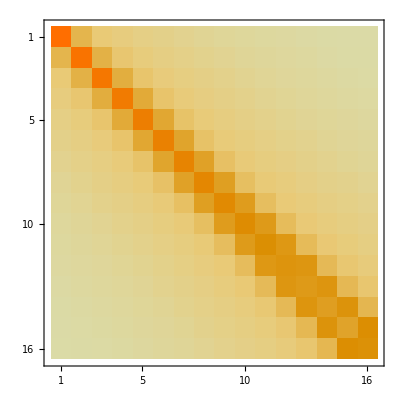

```mathematica
MatrixPlot[MatEl2]
```

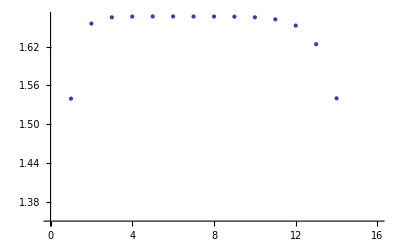

```mathematica
ListPlot[Table[ Sum[MatEl2 [[j,m]],{m,1,16}],{j,1,16}]]
```